```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/subhajit/Dropbox/harmonics

```mathematica
hp2=-(1+c^2)+x/6((19+9 c^2-2 c^4)-eta(19-11 c^2-6 c^4));
```

```mathematica
hp4=-4/3 x s^2(1+c^2)(1-3 eta);
```

```mathematica
hc2=-2 c +(c x)/3((17-4 c^2)-eta (13-12 c^2));
```

```mathematica
hc4=-8/3 x(1-3 eta)c s^2 ;
```

```mathematica
G=6.674 10^-11;
```

```mathematica
c1=2.99792 10^8;
```

```mathematica
yr=3.154 10^7;
```

```mathematica
MS=1.989 10^30;
```

```mathematica
f1=10^-8.33;f2=10^-8.03;A1=10^-6.75;A2=10^-7.2;
```

```mathematica
omg=f1/2 2 Pi
```

1.46943×10^-8

```mathematica
x=((G M MS omg)/c1^3)^(2/3)
```

1.73703×10^-9 M^(2/3)

```mathematica
(*theta=theta Pi/180;*)
(*M=1.5 10^13;*)
```

```mathematica
s=Sin[theta];c=Cos[theta];
```

```mathematica
eta=1/4;
```

```mathematica
A1/A2
```

2.81838

```mathematica
ratiop=hp4/hp2/.M->p1^(3/2)//PowerExpand
```

-(5.7901×10^-10 p1 (1+Cos[theta]^2) Sin[theta]^2)/(-1-Cos[theta]^2+2.89505×10^-10 p1 (19+9 Cos[theta]^2-2 Cos[theta]^4+1/4 (-19+11 Cos[theta]^2+6 Cos[theta]^4)))

```mathematica
ratiox=hc4/hc2/.M->p2^(3/2)//PowerExpand
```

-(1.15802×10^-9 p2 Cos[theta] Sin[theta]^2)/(-2 Cos[theta]+5.7901×10^-10 p2 Cos[theta] (17-4 Cos[theta]^2+1/4 (-13+12 Cos[theta]^2)))

```mathematica
solvep=Solve[ratiop==A2/A1,p1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1→-(3.8336×10^34 (3.+Cos[2. theta]))/(-5.2075×10^26-6.22982×10^25 Cos[2. theta]+1.70272×10^25 Cos[4. theta])}}

```mathematica
solvex=Solve[ratiox==A2/A1,p2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p2→-(1.92059×10^17)/(-8.93433×10^8+1.84508×10^8 Cos[2. theta])}}

```mathematica
finalp=p1^(3/2)/.solvep[[1]]/.theta->theta1 Pi/180
```

7.50603×10^51 (-(3.+Cos[0.0349066 theta1])/(-5.2075×10^26-6.22982×10^25 Cos[0.0349066 theta1]+1.70272×10^25 Cos[0.0698132 theta1]))^(3/2)

```mathematica
finalx=p2^(3/2)/.solvex[[1]]/.theta->theta1 Pi/180
```

8.41687×10^25 (-1/(-8.93433×10^8+1.84508×10^8 Cos[0.0349066 theta1]))^(3/2)

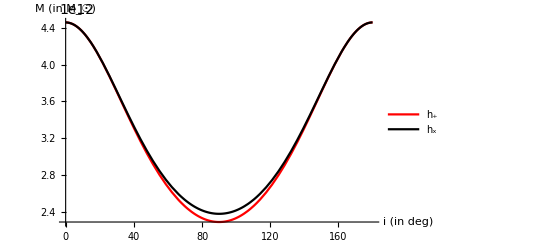

```mathematica
plot=Plot[{finalp,finalx},{theta1,0, 180},PlotStyle->{Red,Black},PlotLegends->{"h_+","h_x"},AxesLabel->{"i (in deg)","M (in M_☉)"}]
```

```mathematica
Export["Harmonics_siyuan.png",plot,ImageResolution->500]
```

Harmonics_siyuan.png

```mathematica
f3=10^-7.7;A3=10^-7.7;
```

```mathematica
nu=10^-8.63;Anu=10^-6.5;
```

```mathematica
1/(nu yr)
```

13.525

```mathematica
1/(f1 yr)
```

6.77857

```mathematica
1/(f2 yr)
```

3.39733